```mathematica
Zip[a_,b_]:=MapIndexed[({#1,b[[First[#2]]]})&,a];
```

```mathematica
ToEdges[Uk_]:= Module[
{mapSet},
mapSet[s_]:=(#[[1]]->#[[2]])&/@s;
Return[mapSet/@Uk];
];
```

```mathematica
ShowMultiGraph[Uk_, styles_]:=Module[
{edges, styleSet},
styleSet[s_] := (Style[#,s[[2]]])&/@s[[1]];
edges = Catenate[ styleSet/@Zip[Uk,styles]];
Return[Graph[edges]];
];
```

{{1->2,2->3},{3->1}}

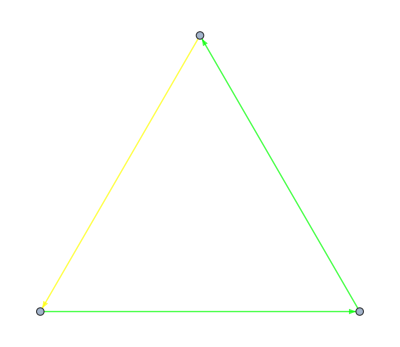

```mathematica
S={{1->2,2->3 },{3->1 }}
ShowMultiGraph[S,{Green,Yellow}]
```